```mathematica
Clear["Global`*"];
(* plot the neutron flux for a 2 group energy structur in a fixed domain *)

d1a=1.2627;sr1a=0.02619;sf1a=0.00848;sf2a=0.07514;
d2a=0.3543;sr2a=0.1210;sr12a=0.0412;

d1b=1.13;sr1b=0.0498;
d2b=0.16;sr2b=0.0197;sr12b=0.0494;

keff=1;

l=20.0;
Nmax=20;h=l/(Nmax-1);
Nleft=5;Nright=16;Ndown=5;Nup=16;
sxminus=0.0;sxplus=0.0;syminus=0.0;syplus=0.0;
(* init sources *)
For[i1=1,i1≤Nmax,i1++,For[j1=1,j1≤Nmax,j1++,source1[i1,j1]=1]];
For[i1=1,i1≤Nmax,i1++,For[j1=1,j1≤Nmax,j1++,source2[i1,j1]=1]];

(* interation loop *)
For[g1=1,g1<8,g1++,
(* diffusion equation in region A for group 1*) etemp1A={u1[i,j]==1/(4*(d1a/h^2)+sr1a)*(sf1a*source1[i,j]/keff+sf2a*source2[i,j]/keff+(d1a/h^2)*(u1[i+1,j]+u1[i-1,j])+(d1a/h^2)*(u1[i,j-1]+u1[i,j+1]))}; 

(* diffusion equation in region A for group 2*) etemp2A={u2[i,j]==1/(4*(d2a/h^2)+sr2a)*(sr12a*u1[i,j]+(d2a/h^2)*(u2[i+1,j]+u2[i-1,j])+(d2a/h^2)*(u2[i,j-1]+u2[i,j+1]))}; 

(* diffusion equation in region B for group 1*)
etemp1B={u1[i,j]==1/(4*(d1b/h^2)+sr1b)*(0+(d1b/h^2)*(u1[i+1,j]+u1[i-1,j])+(d1b/h^2)*(u1[i,j-1]+u1[i,j+1]))};

(* diffusion equation in region B for group 2*)
etemp2B={u2[i,j]==1/(4*(d2b/h^2)+sr2b)*(sr12b*u1[i,j]+(d2b/h^2)*(u2[i+1,j]+u2[i-1,j])+(d2b/h^2)*(u2[i,j-1]+u2[i,j+1]))};

(* boundary condition at the transition from region A to B for group 1*)
etemp1ABleft={u1[i,j]==1/(d1a/h+d1b/h)*((d1a/h)*(u1[i+1,j])+(d1b/h)*(u1[i-1,j]))};
etemp1ABright={u1[i,j]==1/(d1a/h+d1b/h)*((d1b/h)*(u1[i+1,j])+(d1a/h)*(u1[i-1,j]))};
etemp1ABdown={u1[i,j]==1/(d1a/h+d1b/h)*((d1a/h)*(u1[i,j+1])+(d1b/h)*(u1[i,j-1]))};
etemp1ABup={u1[i,j]==1/(d1a/h+d1b/h)*((d1b/h)*(u1[i,j+1])+(d1a/h)*(u1[i,j-1]))};
(* boundary condition at the transition from region A to B for group 2*)
etemp2ABleft={u2[i,j]==1/(d2a/h+d2b/h)*((d2a/h)*(u2[i+1,j])+(d2b/h)*(u2[i-1,j]))};
etemp2ABright={u2[i,j]==1/(d2a/h+d2b/h)*((d2b/h)*(u2[i+1,j])+(d2a/h)*(u2[i-1,j]))};
etemp2ABdown={u2[i,j]==1/(d2a/h+d2b/h)*((d2a/h)*(u2[i,j+1])+(d2b/h)*(u2[i,j-1]))};
etemp2ABup={u2[i,j]==1/(d2a/h+d2b/h)*((d2b/h)*(u2[i,j+1])+(d2a/h)*(u2[i,j-1]))};

(* boundary condition at the boundary of B  for group 1*)
rd1Bleft=Table[u1[1,j]==sxminus,{j,1,Nmax}];
rd1Bright=Table[u1[Nmax,j]==sxplus,{j,1,Nmax}];
     rd1Bdown=Table[u1[i,1]==syminus,{i,2,Nmax-1}];
     rd1Bup=Table[u1[i,Nmax]==syplus,{i,2,Nmax-1}];
(* boundary condition at the boundary of B  for group 2*)
rd2Bleft=Table[u2[1,j]==sxminus,{j,1,Nmax}];
rd2Bright=Table[u2[Nmax,j]==sxplus,{j,1,Nmax}];
     rd2Bdown=Table[u2[i,1]==syminus,{i,2,Nmax-1}];
     rd2Bup=Table[u2[i,Nmax]==syplus,{i,2,Nmax-1}];

(* collect all equations here for group 1*)
eqns1B1=Table[etemp1B,{i,2,Nleft-1},{j,2,Nmax-1}]//Flatten;
eqns2B1=Table[etemp1B,{i,Nright+1,Nmax-1},{j,2,Nmax-1}]//Flatten;
eqns3B1=Table[etemp1B,{i,Nleft,Nright},{j,2,Ndown-1}]//Flatten;
eqns4B1=Table[etemp1B,{i,Nleft,Nright},{j,Nup+1,Nmax-1}]//Flatten;

eqns1A=Table[etemp1A,{i,Nleft+1,Nright-1},{j,Ndown+1,Nup-1}]//Flatten;

rd1Aleft=Table[etemp1ABleft,{i,{Nleft}},{j,Ndown,Nup}]//Flatten;
rd1Aright=Table[etemp1ABright,{i,{Nright}},{j,Ndown,Nup}]//Flatten;
     rd1Adown=Table[etemp1ABdown,{i,Nleft+1,Nright-1},{j,{Ndown}}]//Flatten;
     rd1Aup=Table[etemp1ABup,{i,Nleft+1,Nright-1},{j,{Nup}}]//Flatten;

syseqns1=Union[Join[eqns1B1,eqns2B1,eqns3B1,eqns4B1,eqns1A,rd1Bleft,rd1Bright,rd1Bdown,rd1Bup,rd1Aleft,rd1Aright,rd1Adown,rd1Aup]];
var1=Union[Cases[syseqns1, u1[_,_],∞]]; (*  Print["var1: ",Length[var1],"  ",Length[syseqns1]]; *)

(* collect all equations here for group 2*)
eqns1B2=Table[etemp2B,{i,2,Nleft-1},{j,2,Nmax-1}]//Flatten;eqns2B2=Table[etemp2B,{i,Nright+1,Nmax-1},{j,2,Nmax-1}]//Flatten;
eqns3B2=Table[etemp2B,{i,Nleft,Nright},{j,2,Ndown-1}]//Flatten;
eqns4B2=Table[etemp2B,{i,Nleft,Nright},{j,Nup+1,Nmax-1}]//Flatten;

eqns2A=Table[etemp2A,{i,Nleft+1,Nright-1},{j,Ndown+1,Nup-1}]//Flatten;

rd2Aleft=Table[etemp2ABleft,{i,{Nleft}},{j,Ndown,Nup}]//Flatten;
rd2Aright=Table[etemp2ABright,{i,{Nright}},{j,Ndown,Nup}]//Flatten;
     rd2Adown=Table[etemp2ABdown,{i,Nleft+1,Nright-1},{j,{Ndown}}]//Flatten;
     rd2Aup=Table[etemp2ABup,{i,Nleft+1,Nright-1},{j,{Nup}}]//Flatten;

syseqns2=Union[Join[eqns1B2,eqns2B2,eqns3B2,eqns4B2,eqns2A,rd2Bleft,rd2Bright,rd2Bdown,rd2Bup,rd2Aleft,rd2Aright,rd2Adown,rd2Aup]];
var2=Union[Cases[syseqns2, u2[_,_],∞]]; (* Print["var2: ",Length[var2],"  ",Length[syseqns2]]; *)

syseqns=Join[syseqns1,syseqns2];var=Join[var1,var2];
{p,A}=CoefficientArrays[syseqns,var];
mysol=LinearSolve[A,-p];
mysol1=Partition[Take[mysol,{1,400}],Nmax]; 
mysol2=Partition[Take[mysol,{401,800}],Nmax]; 

(*integral over sf1*phi_new *)
k1=0;
For[i1=Nleft+1,i1≤Nright-1,i1++,For[j1=Ndown+1,j1≤Nup-1,j1++,k1=k1+(sf1a*source1[i1,j1]+sf2a*source2[i1,j1])/(keff*(4*(d1a/h^2)+sr1a))]];

(*integral over sf1*phi_old/keff_old=A*phi_old *)
For[i1=1,i1≤Nmax,i1++,For[j1=1,j1≤Nmax,j1++,source1[i1,j1]=mysol1[[i1]][[j1]]]]; 
For[i1=1,i1≤Nmax,i1++,For[j1=1,j1≤Nmax,j1++,source2[i1,j1]=mysol2[[i1]][[j1]]]]; 

k2=0;
For[i1=Nleft+1,i1≤Nright-1,i1++,For[j1=Ndown+1,j1≤Nup-1,j1++,k2=k2+(sf1a*source1[i1,j1]+sf2a*source2[i1,j1]);]] ;
keff=(k2/k1);

Print[keff," ",Norm[mysol]];
];

(* ListPlot3D[Table[source1[i1,j1],{i1,1,Nmax},{j1,1,Nmax}]] *)
(*  ListPlot[Normalize[Table[source[i1,10],{i1,1,Nmax}]],Joined->True] *)
keff
```

1.48529 9.86359

1.50443 2.17489

1.50654 0.474969

1.50678 0.103616

1.5068 0.0226016

1.50681 0.00492998

1.50681 0.00107535

1.50681

```mathematica
ListPlot3D[Table[source1[i1,j1],{i1,1,Nmax},{j1,1,Nmax}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[source2[i1,j1],{i1,1,Nmax},{j1,1,Nmax}]]
```

-Graphics3D-

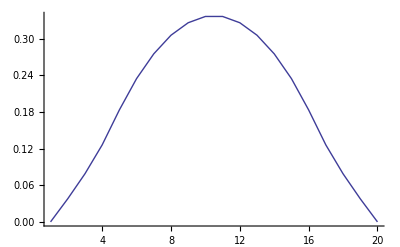

```mathematica
ListPlot[Normalize[Table[source1[i1,10],{i1,1,Nmax}]],Joined->True]
```

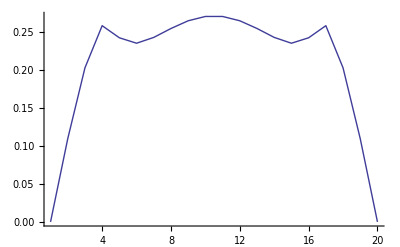

```mathematica
ListPlot[Normalize[Table[source2[i1,10],{i1,1,Nmax}]],Joined->True]
```

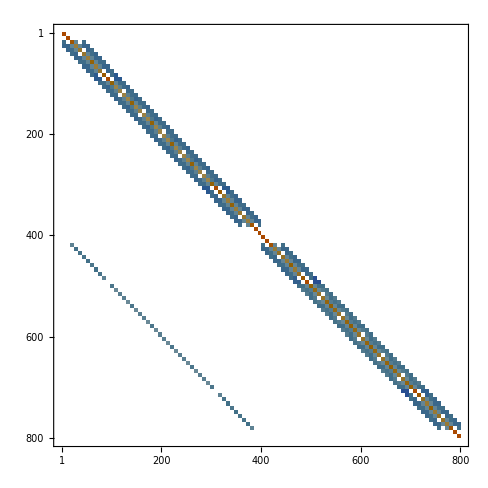

```mathematica
MatrixPlot[A]
```